This Mathematica notebook is included with FastEEC, which provides a fast evaluation of higher-point energy correlators.

### Load MaTeX

Used for latex plot axes

```mathematica
ResourceFunction["MaTeXInstall"][]
<<MaTeX`
```

PacletObject[…]

### Read input

Set directory to the notebook directory, which contains examples of output files.

```mathematica
SetDirectory[NotebookDirectory[]];
```

List of labels and corresponding filenames that need to be read. The full file is generated using the available energy correlators
package by Komiske. 

For our fast method, the files listed below can be generated by executing the following from the terminal:
./eec_fast ../data.txt 100000 4 8 -5 75 test_4pt_8.out
./eec_fast ../data.txt 100000 4 32 -5 75 test_4pt_32.out
./eec_fast ../data.txt 100000 4 64 -5 75 test_4pt_64.out
./eec_fast_kt ../data.txt 100000 4 1 -5 75 test_4pt_1_kt.out

```mathematica
label={full,res8,res32,res64,res1kt};filenames={"test_4pt.out","test_4pt_8.out","test_4pt_32.out","test_4pt_64.out","test_4pt_1_kt.out"};
```

Read files for E4C that are included:

```mathematica
Module[{f},
Do[{
f=filenames[[i]];
nevent =Read[f,Number];
nbins =Read[f,Number];
minbin =Read[f,Real];
maxbin=Read[f,Real];
res[label[[i]]]=Read[f,Table[Real,nbins]];
Close[f];
},{i,1,Length[label]}];
xvalues=Table[10^(minbin+(i-0.5)/nbins(maxbin-minbin)),{i,1,nbins}];];
```

### Histogram routines

Routine to reduce the number of bins of histogram listin by a factor fac.

```mathematica
rebinin[listin_,fac_]:=Block[{listnew,xnew,x,x2},
xnew={};
x=Partition[listin,fac];
x2=Table[Mean[x[[i]]],{i,1,Length[x]}];
AppendTo[xnew,x2];Return[xnew[[1]]];]
```

Routine to normalize the histogram with label lab such that the area under the curve (integral) is 1.

```mathematica
maketabnorm[lab_]:=Transpose[{xvalues,(res[lab]*nbins)/(Total[res[lab]]*(maxbin-minbin))}];
```

Calculate the difference between the histogram with label lab and the histogram with label full, reducing the number of bins of the result by a factor fac.

```mathematica
makeratioreb[lab_,fac_]:=Transpose[{rebinin[maketabnorm[lab][[;;,1]],fac],100*(rebinin[res[lab],fac]/(rebinin[res[full],fac]+10^(-20))-1)}][[2;;Floor[(nbins/fac)]-1]];(* Added a small number to denominator to avoid division by zero. *)
```

### E4C plots

Comparing different approximations against the full calculation.
The overflow and underflow bins are removed, and the histograms are normalized.

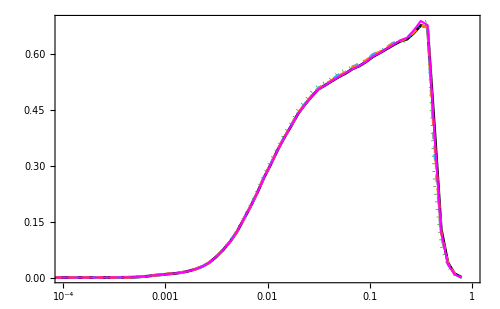

```mathematica
fourp=ListLogLinearPlot[Evaluate[Table[maketabnorm[label[[i]]][[2;;nbins-1]],{i,1,Length[label]}]],
PlotStyle->{{Black,Thickness[0.004]},{Darker[Green],Dotted},{RGBColor[0.2,0.67,1],DotDashed},{Orange,Dashed},{Magenta,Thickness[0.003]}},Joined->True,PlotLegends->Placed[{MaTeX["\\text{full}",Magnification->1.3],MaTeX["\\text{C/A, $f=8$}",Magnification->1.3],MaTeX["\\text{C/A, $f=32$}",Magnification->1.3],MaTeX["\\text{C/A, $f=64$}",Magnification->1.3],MaTeX["\\text{k$_{\\text T}$, $f=\\text{k}_{\\text T,{\\text{min}}}^{\\text{2}}$}",Magnification->1.3]},{Left,Top}],PlotRange->{{10^-4,1},Automatic},Frame->True,ImageSize->500,FrameLabel->{MaTeX["\\text{$R_{L}$}",Magnification->1.5],
MaTeX["\\text{P$^{4}$EC (normalized)}",Magnification->1.5]}]
```

Plot the relative error between different approximations. We reduce the number of bins by a factor of 2 to reduce the statistical fluctuations:

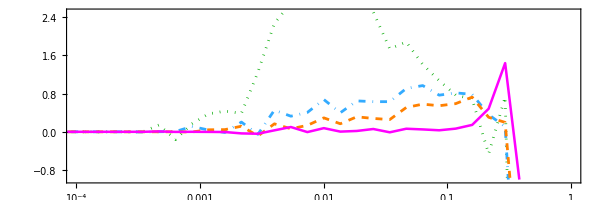

```mathematica
fourpdiffreb=ListLogLinearPlot[Evaluate[Table[makeratioreb[label[[i]],2],{i,2,Length[label]}]],
PlotStyle->{{Darker[Green],Dotted},{RGBColor[0.2,0.67,1],DotDashed},{Orange,Dashed},{Magenta,Thickness[0.003]}},Joined->True,PlotRange->{{10^-4,1},{-1,2.5}},Frame->True,ImageSize->605.15,FrameLabel->{
MaTeX["\\text{$R_{L}$}",Magnification->1.5],MaTeX["\\text{fast}-\\text{full} [\\%]",Magnification->1.5]
},AspectRatio->1/3]
```